# Exercises

For the exam complete two of these... 
Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.
Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.
Q3: Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.
Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].
Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)


Q1:

```mathematica
f[x_]:=x*Exp[-x]+x(1-x)
```

```mathematica
f[0]
f[0.1]
f[0.2]
f[0.4]
f[0.8]
```

0

0.180484

0.323746

0.508128

0.519463

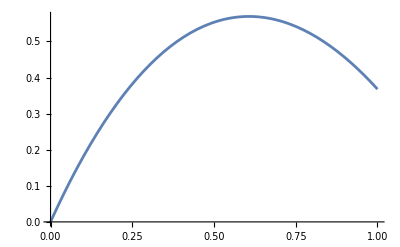

```mathematica
Plot[f[x],{x,0,1}]
```

Q3:

```mathematica
f[x_]:=Sin[x] Exp[-x]
Integrate[f[x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
F[x_] := Integrate[f[x],x]
D[F[x],x]
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[D[F[x],x]]
```

ⅇ^-x Sin[x]